```mathematica
Solve[{(k1+k2-ω^2 m1 )x1-k2 x2==F1,-k2 x1+(k2-ω^2m2)x2==0},{x1,x2}]//Simplify
```

{{x1→(F1 (-k2+m2 ω^2))/(k1 (-k2+m2 ω^2)+ω^2 (k2 (m1+m2)-m1 m2 ω^2)),x2→(F1 k2)/(k1 (k2-m2 ω^2)+ω^2 (-k2 (m1+m2)+m1 m2 ω^2))}}

```mathematica
(k1+k2-ω^2 m1)(k2-ω^2m2)-k2^2//FullSimplify
-(k1 (-k2+m2 ω^2)+ω^2 (k2 (m1+m2)-m1 m2 ω^2))//FullSimplify
```

k1 k2-(k1 m2+k2 (m1+m2)) ω^2+m1 m2 ω^4

k1 k2-(k1 m2+k2 (m1+m2)) ω^2+m1 m2 ω^4

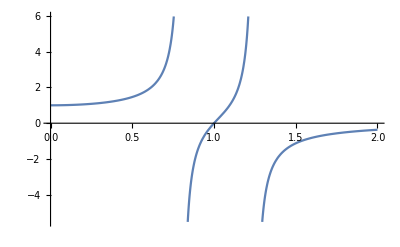

```mathematica
Plot[(1-x^2)/((1+0.2-x^2)(1-x^2)-0.2),{x,0,2}]
```

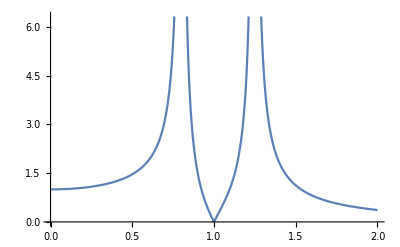

```mathematica
Plot[Abs[(1-x^2)/((1+0.2-x^2)(1-x^2)-0.2)],{x,0,2}]
```